# Rectangular Test Region

## Introduction

Solution of River Growth problem using Laplace equation is sophisticated task. 
There are probably a lot of ways to solve them, but here is presented FEM method.

FEM method include:
 - Geometry setup.
 - Mesh generation.
 - PDE solver.
 - Integration over tip points.
 
 Each of these steps contains a lot of parameters which influence time of evaluation and precision in different rates. So let light all these aspects.
 
 Here is presented basic square region which is good simplification of River Growth model.

## Framework

Here is implemented all necessary base function:
 - Boundary generation
 - Mesh generation
 - Solution
 - Integral over whole region.
 - Integral over circular region with centrum in tip.
 - Maximal value of function
 - Series Parameters

## version 1.0.0

## Formula of relative difference in percentage

```mathematica
PercentageDifference[a_, b_]:=Abs[a-b]/Max[a,b]100.;
PercentageDifferenceString[a_, b_]:=ToString[Abs[a-b]/Max[a,b]100.]<>"%";
PercentageDifferenceString[1, 1] 
PercentageDifferenceString[0.4, 1]
```

0.%

60.%

## PDE setup

### Package Import

```mathematica
Needs["NDSolve`FEM`"]
```

### Region Mesh

```mathematica
(*Boundaries*)
Clear[rectangulraBoundary]
rectangulraBoundary[TipPoint_/;MatchQ[TipPoint,{_Real,_Real}],width_Real:1.,height_Real:1.] :=Association[ 
"tip"->TipPoint,
"boundary"->ToBoundaryMesh[
"Coordinates"->{
{0,0},
{TipPoint[[1]],0},
TipPoint,
{width,0},
{width,height},
{0,height}
},
"BoundaryElements"->{
LineElement[{
{1,2},
{2,3},
{2,4},
{4,5},
{5,6},
{6,1}},
{2,2,2,2,2,2}
]
}
]
]

(*Mesh Generation*)
Clear[defaultMeshRefinmentFunc]
defaultMeshRefinmentFunc[
TipPoint_/;MatchQ[TipPoint,{_Real,_Real}],
gain_Real:0.0001]:= 
Function[
{
vertices,area
},
(area ≥1. 10^-10+Exp[gain Min[Norm[TipPoint-#]&/@vertices]]-1)
];

Clear[regionMesh]
regionMesh[boundary_Association, meshRefinmentFunc_Function:Function[{vertices,area},False]]:=
Association["tip"->boundary["tip"],
"mesh"->ToElementMesh[
boundary["boundary"],
"MeshQualityGoal"->"Maximal",
MaxCellMeasure->1,
MeshRefinementFunction->meshRefinmentFunc
]
];

(*PDE Solving*)
Clear[solution]
solution[
mesh_Association,
accuracy_Integer:25]:=
Module[
{
bounds = mesh["mesh"]["Bounds"],
tipPoint=mesh["tip"],
u,x,y
},
NDSolveValue[
{
Laplacian[u[x,y],{x,y}]+1==0,
{
DirichletCondition[
u[x,y]==0,
x≤bounds[[1,1]]||x≥bounds[[1,2]]||y≤bounds[[2,1]]||y≥bounds[[2,2]]],
DirichletCondition[
u[x,y]==0,
x==tipPoint[[1]]&&y≥bounds[[2,1]]&&y≤tipPoint[[2]]]
}
},
u,
{x,y}∈mesh["mesh"],
AccuracyGoal->accuracy,
PrecisionGoal->accuracy]
];
```

<|tip→{0.25,0.1},boundary→ElementMesh[{{0.,1.},{0.,1.}},Automatic]|>

<|tip→{0.25,0.1},mesh→ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<4944>]}]|>

InterpolatingFunction[…]

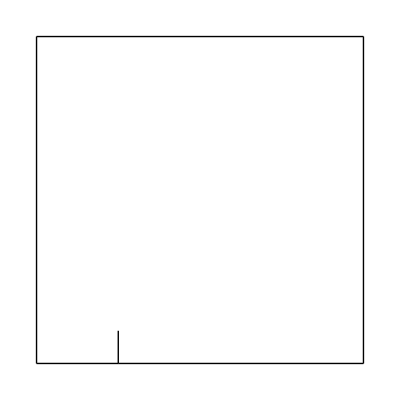
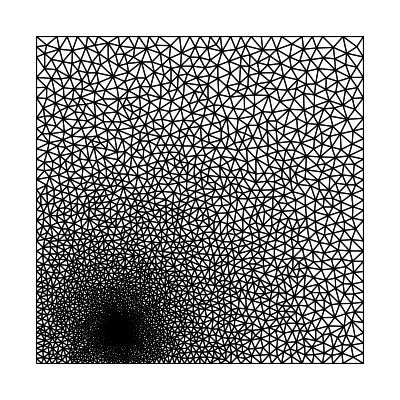
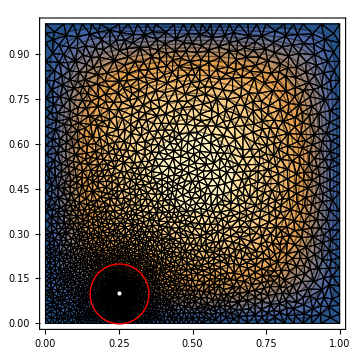

```mathematica
bd=rectangulraBoundary[{0.25,0.1}]
msh=regionMesh[bd,defaultMeshRefinmentFunc[bd["tip"],0.001]]
sol=solution[msh]
Row[{
bd["boundary"]["Wireframe"],
msh["mesh"]["Wireframe"],
Show[ContourPlot[sol[x,y],{x,y}∈msh["mesh"],Contours->20, ImageSize->Medium],
msh["mesh"]["Wireframe"],
Graphics[{
Red, Circle[{0.25,0.1},0.1], 
White, Point[{0.25,0.1}]}]
]
}]
```

### Test Values Functions

```mathematica
WholeRegionIntegral[
solution_InterpolatingFunction,
accuracy_Integer:6]:=
NIntegrate[
solution[x,y],
{x,y}∈solution["ElementMesh"],
AccuracyGoal->accuracy,
PrecisionGoal->accuracy];


TipCircleIntegral[
solution_InterpolatingFunction,
TipPoint_/;MatchQ[TipPoint,{_Real,_Real}],
accuracy_Integer:6]:=
NIntegrate[
solution[x,y],
{x,y}∈Disk[TipPoint,0.1],
AccuracyGoal->20,
PrecisionGoal->15];


MaximalValue[solution_InterpolatingFunction]:=
NMaxValue[
solution[x,y],
{x,y}∈solution["ElementMesh"]
];
```

```mathematica
msh=regionMesh[
rectangulraBoundary[{0.25,0.1}],
defaultMeshRefinmentFunc[{0.25,0.1},0.0001]
];
sol=solution[msh];

RealDigits[WholeRegionIntegral[sol]]
RealDigits[TipCircleIntegral[sol,{0.25,0.1}]]//Quiet
RealDigits[MaximalValue[sol]]//Quiet
```

{{3,4,2,0,2,0,1,8,8,6,7,6,2,9,2,2},-1}

{{4,6,1,1,3,7,4,2,8,1,6,7,8,6,5,1},-3}

{{7,2,5,7,9,2,1,3,1,4,4,4,9,9,1,0},-1}

## Series Parameters(Using same formula as from FreeFem++ implementation)

```mathematica
BaseVector[
nf_Integer/;nf≥1&&nf≤3, 
zf_]:=
If[Mod[nf,2]==0,
-Im[zf^(nf/2.)],
Re[zf^(nf/2.)]
];


BaseVectorModified[
nf_Integer/;MemberQ[{1,2,3},nf], 
tipPoint_/;MatchQ[tipPoint,{_Real,_Real}], 
currentPoint_, 
tipangle_Real:Pi/2.(*stricly vertical*)]:=
BaseVector[nf,Exp[-I tipangle] (currentPoint[[1]]-tipPoint[[1]]+I(currentPoint[[2]]-tipPoint[[2]]))];


weightFunc[
 Rcurrent_,
R_Real:0.01(*same radius is in freefem*),
exp_Real:2.(*value from FreeFem*)]:=
Exp[-(Rcurrent/R)^exp];


seriesParameters[
solution_InterpolatingFunction,
tipPoint_/;MatchQ[tipPoint,{_Real,_Real}], 
accuracy_Integer:14,
exponant_Real:2.(*value from FreeFem*),
radius_Real:0.01(*same radius is in freefem*),
tipangle_Real:Pi/2.(*stricly vertical*)]:=
NIntegrate[
solution[x,y] 
weightFunc[Norm[{x,y}-tipPoint],radius,exponant]
{
BaseVectorModified[1, tipPoint, {x,y},tipangle],
BaseVectorModified[2, tipPoint, {x,y},tipangle],
BaseVectorModified[3, tipPoint, {x,y},tipangle]
},
{x,y}∈Disk[tipPoint,3radius],
AccuracyGoal->accuracy, 
PrecisionGoal->accuracy]/
NIntegrate[
weightFunc[Norm[{x,y}-tipPoint],radius,exponant]
{
BaseVectorModified[1, tipPoint, {x,y},tipangle],
BaseVectorModified[2, tipPoint, {x,y},tipangle],
BaseVectorModified[3, tipPoint, {x,y},tipangle]
}^2,
{x,y}∈Disk[tipPoint,3radius],
AccuracyGoal->accuracy, 
PrecisionGoal->accuracy]
```

```mathematica
msh=regionMesh[
rectangulraBoundary[{0.25,0.1}],
defaultMeshRefinmentFunc[{0.25,0.1},0.0001]
]
sol=solution[msh]
Timing[seriesParameters[sol,{0.25,0.1}]]//Quiet
```

<|tip→{0.25,0.1},mesh→ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<45613>]}]|>

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

{20.5625,{0.101883,0.0454659,0.131008}}

## Mesh refinement function

Lets figure out the best mesh refinement function and optimize performance.

#### Evaluate efMeshSizeFunc

use only to update efMeshSizeFunc associations

```mathematica
parameterValues=Table[0.01 0.8^i,{i,0,25,5}];
MeshElementsNumberByParameter[meshRefName_,parameter_]:=
Length@regionMesh[ rectangulraBoundary[{0.25,0.1}],MeshRefinementFunctions[meshRefRulesAssoc][meshRefName][{0.25,0.1},parameter]]["mesh"]["MeshElements"][[1,1]];
tb=Table[MeshElementsNumberByParameter[meshRefName,p],{meshRefName,meshRefRulesAssoc//Keys},{p,parameterValues}];
funcs=Normal@NonlinearModelFit[Transpose[{parameterValues,#}],a*meshSize^n,{a,n},meshSize]&/@tb;
funcsAssoc=Association@MapThread[#1->#2&,{meshRefRulesAssoc//Keys,funcs}];
```

#### Definitions

```mathematica
Clear[meshRefRulesAssoc]
meshRefRulesAssoc:=Association[
"Uniform"->Function[{gain,r},gain/2],
"Linear"->Function[{gain,r},gain r],
"SquareRoot"->Function[{gain,r},gain √r],
"2/3 Power"->Function[{gain,r},gain r^(2/3)],
"3/2 Power"->Function[{gain,r},gain r^(3/2)],
"Square"->Function[{gain,r},gain r^2],
"Exponent"->Function[{gain,r},Exp[gain r]-1],
"FreeFem"->Function[{gain,r},1/(1+Exp[ - 4gain r ])-1/2]
];

efMeshSizeFunc=Association[
"Uniform"->Function[{efMS},3.65308930195322/efMS^0.9934358992529257],
"Linear"->Function[{efMS},7.189999104965321/efMS^0.9634329953188852],
"SquareRoot"->Function[{efMS},5.457397983103355/efMS^0.9289113920651858],
"2/3 Power"->Function[{efMS},5.47108494823113/efMS^0.9463755604807781],
"3/2 Power"->Function[{efMS},15.594630537307808/efMS^0.985119703483951],
"Square"->Function[{efMS},159.54810370999152/efMS^0.919609117912843],
"Exponent"->Function[{efMS},7.382576707315951/efMS^0.9604883806181944],
"FreeFem"->Function[{efMS},7.189999104965321/efMS^0.9634329953188852]
];

(*Generate Mesh Refinment Fucntions in format suitable for MeshRefinementFunction of ToElementMesh Function*)

Clear[MeshRefinementFunctions]
MeshRefinementFunctions[
meshRefFunctions_Association,
minArea_Real:1. 10^-11]:=
Module[
{funcApply},

funcApply[func_]:=
Function[
{tipPoint,gain},
Function[
{vertices,area},
(area≥minArea+func[gain,Min[Norm[tipPoint-#]&/@vertices]])
]
];

Association@Table[
pair[[1]]->
funcApply[pair[[2]]],
{pair,Normal[meshRefFunctions]}
]
];
```

```mathematica
Manipulate[
Plot[
Evaluate@((#[gain,distance])&/@(Values@meshRefRulesAssoc)),
{distance, 0, 1},
AspectRatio->1,
PlotLegends->Keys@meshRefRulesAssoc,
AxesLabel->{"Distance from tip","Mesh Element Area Constraint"},
PlotRange->All,
ImageSize->Large
],
{gain,0.00001,1}
]
```

#### One of the main performance impact is - number of mesh elements. So lets consider next three things: - Value Precision - Number of Mesh Elements - Evaluation Time

```mathematica
Clear[performanceResearch]
performanceResearch[parameterValues_,targetValueFunction_, meshRefinmentFunc_,tipPoint_:{0.25,0.1}]:=Module[
{
meshesTiming,
meshSize,
meshTime,
meshes,
solutionsTiming,
solutiontValues,
solutionTime
},

meshesTiming = 
Timing[
regionMesh[
rectangulraBoundary[tipPoint],
meshRefinmentFunc[tipPoint,#]
]
]&/@parameterValues;

meshes=meshesTiming[[All,2]];
meshSize=Length[#["mesh"]["MeshElements"][[1,1]]]&/@meshes;
meshTime=meshesTiming[[All,1]];

solutionsTiming=Timing[
targetValueFunction[
solution[
#
]
]
]&/@meshes;
solutiontValues=solutionsTiming[[All,2]];
solutionTime=solutionsTiming[[All,1]];

Association["parameterValues"->parameterValues,"meshSize"->meshSize,"meshTime"->meshTime ,"solutionValues"->solutiontValues,"solutionTime"->solutionTime]
]

MainCharacteristics=Association[
"MeshElementsNumberByParameter"->{"parameterValues","meshSize"},
"MeshingTime"->{"meshTime","meshSize"},
"SolutionTime"->{"meshSize","solutionTime"},
"Perfomance"->{"meshSize","solutionValues"}
];

Clear[GeneratePlots];
GeneratePlots[plotType_String,meshRefFuncCharacteristics_Association ]:=Module[
{
plotLegends = Keys@meshRefFuncCharacteristics,
xAxisTitle=First[MainCharacteristics[plotType]],
yAxisTitle=Last[MainCharacteristics[plotType]],
plotData
},

plotData = Transpose[{#[xAxisTitle],#[yAxisTitle]}]&/@meshRefFuncCharacteristics;
ListLogLogPlot[plotData,
Joined->True,
PlotLabel->plotType,
AxesLabel->{xAxisTitle,yAxisTitle},
PlotRange->All,
ImageSize->Large
]
]
```

### Function parameter as function of mesh elements number: target Value WholeRegionIntegral

```mathematica
meshRefFuncCharacteristics[range_/;MatchQ[range,{_Integer,_Integer,_Integer}],targetValueFunction_:WholeRegionIntegral]:=
MapThread[
performanceResearch[#1,targetValueFunction,#2]&,
{Association[
(#->Table[efMeshSizeFunc[#][i],{i,range[[1]],range[[2]],range[[3]]}])&/@Keys[meshRefRulesAssoc]
],
MeshRefinementFunctions[meshRefRulesAssoc]
}
];
```

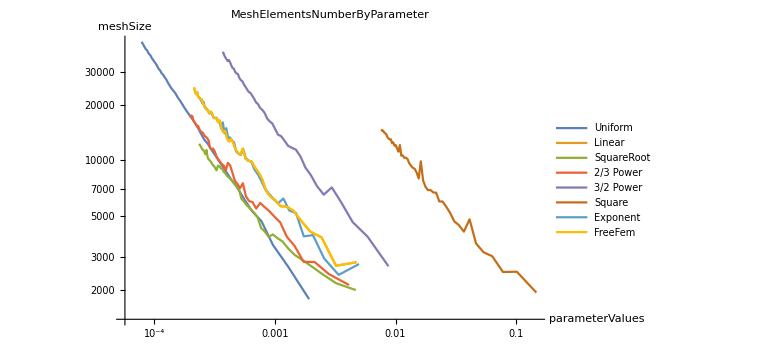
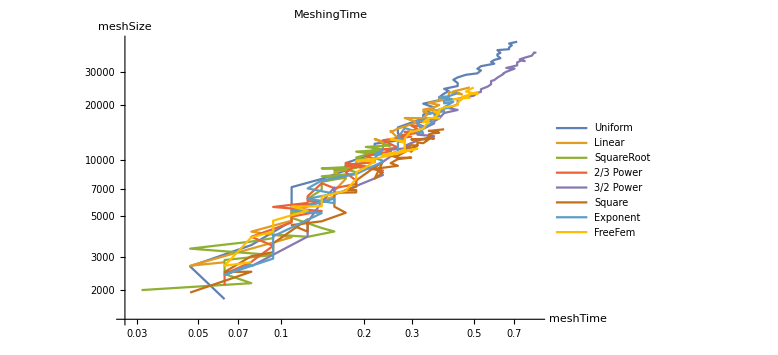
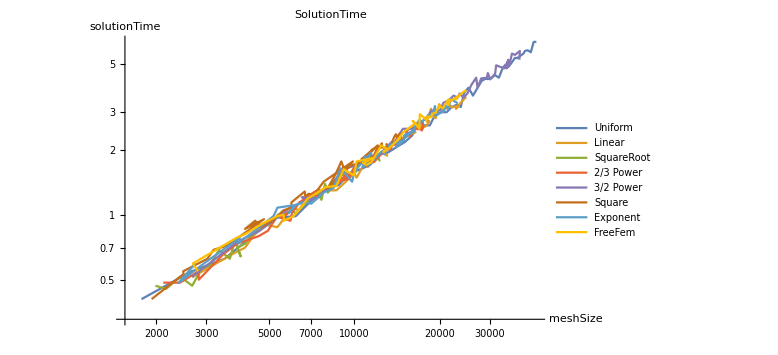
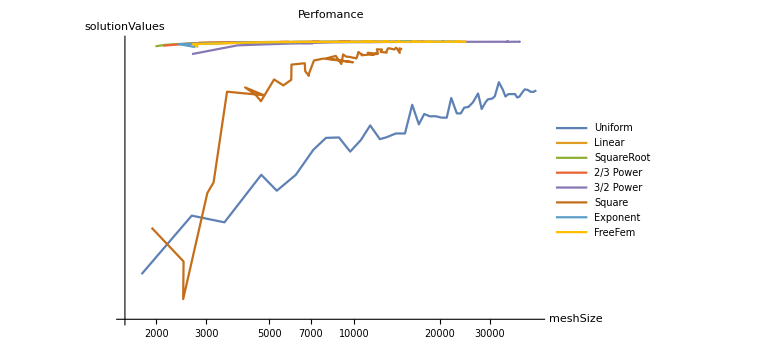

```mathematica
ch=meshRefFuncCharacteristics[{2000,50000,1000},WholeRegionIntegral];
GeneratePlots[#,ch]&/@Keys@MainCharacteristics//Column
```

#### As can be seen from above plots.. Uniform and Square gives the worst results, let drop them.

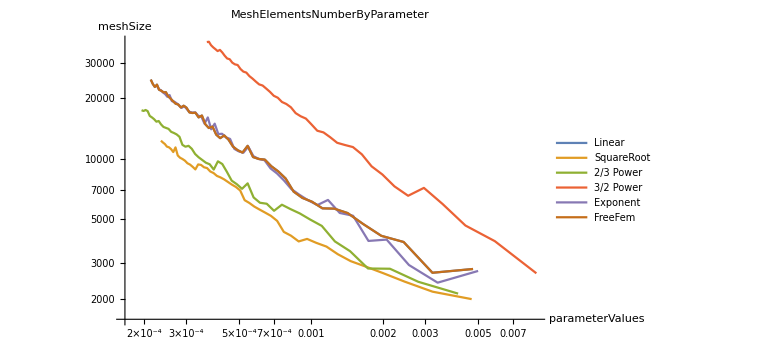
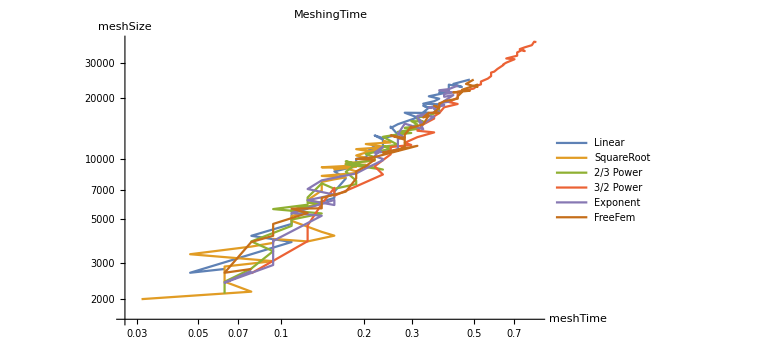
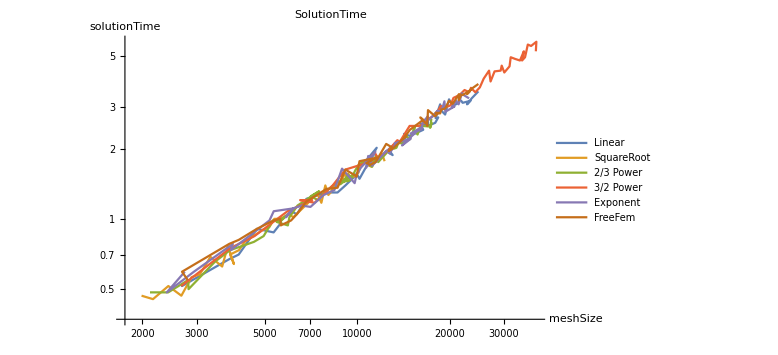
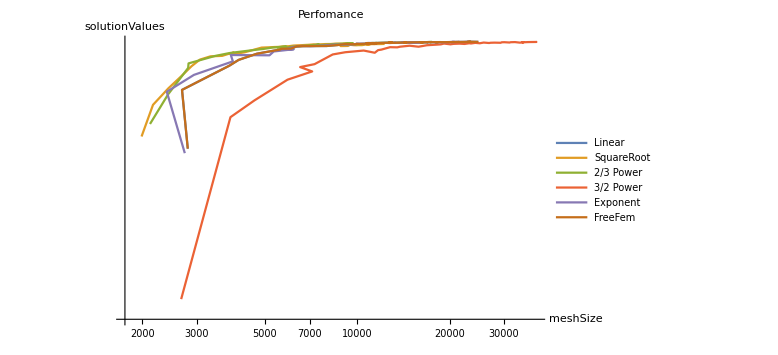

```mathematica
chDropped=KeyDrop[ch,{"Uniform","Square","3/2 Power"}];
GeneratePlots[#,chDropped]&/@Keys@MainCharacteristics//Column
```

#### So the best yet mesh constraint function is simple SquareRoot and 2/3 Power

### Function parameter as function of mesh elements number: target Value TipCircleIntegral

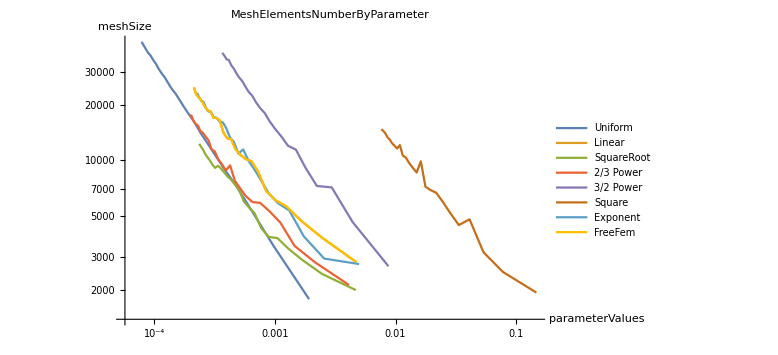
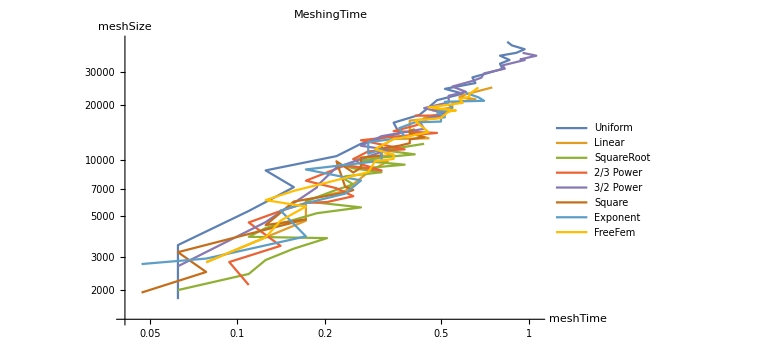
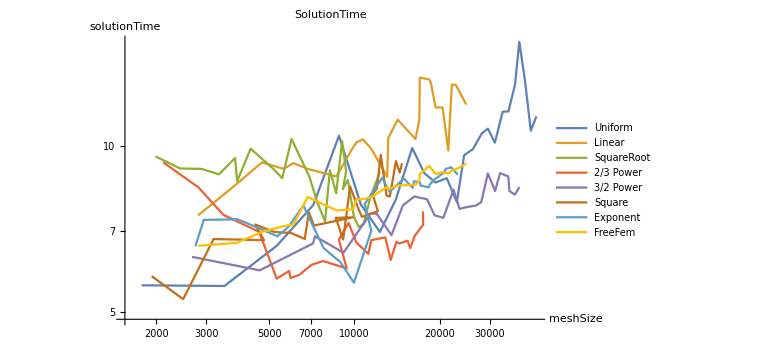
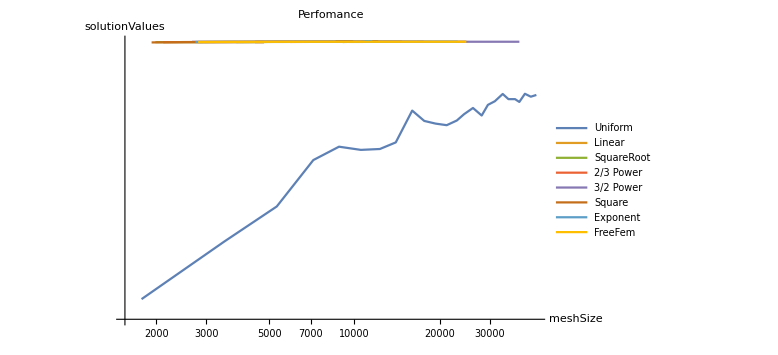

```mathematica
ch=meshRefFuncCharacteristics[{2000,50000,2000},TipCircleIntegral[#,{0.25,0.1}]&]//Quiet;
GeneratePlots[#,ch]&/@Keys@MainCharacteristics//Column
```

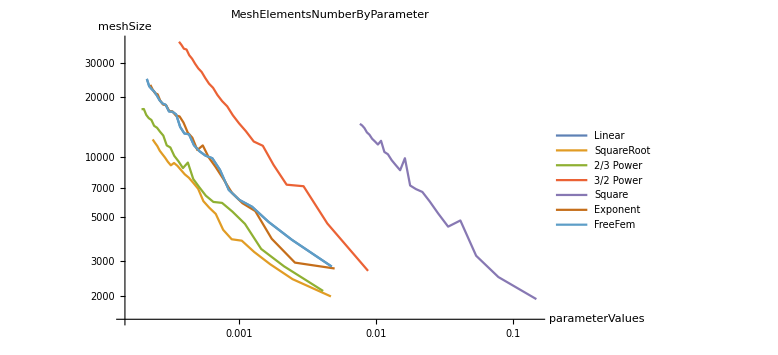
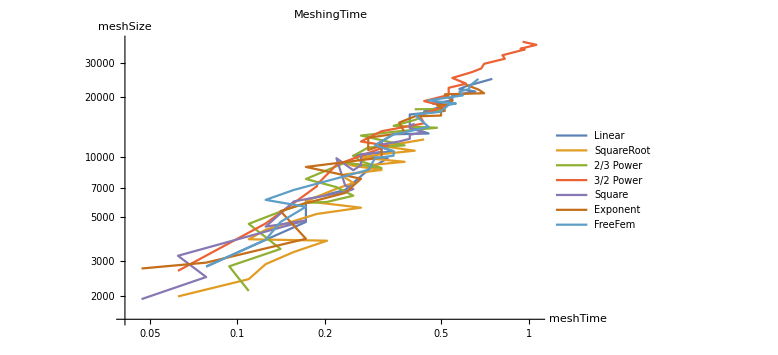
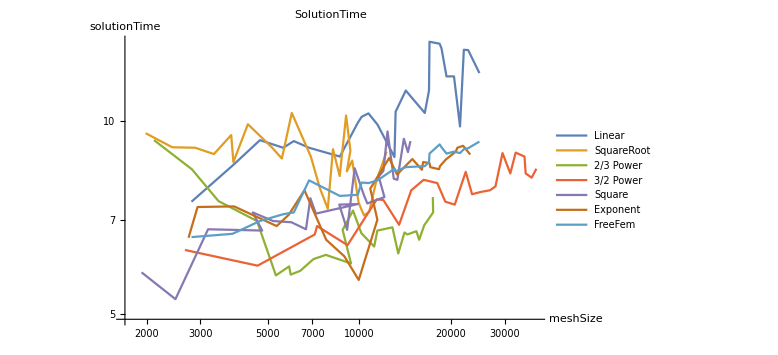
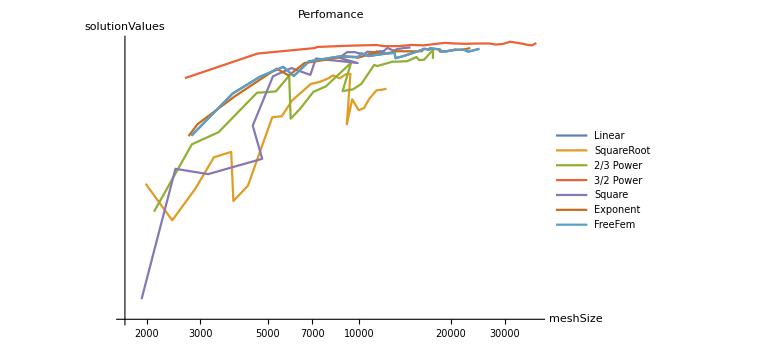

```mathematica
chDropped=KeyDrop[ch,{"Uniform"}];
GeneratePlots[#,chDropped]&/@Keys@MainCharacteristics//Column
```

## Similar work about circle region Integration

```mathematica
Clear[GetTipMesh]
GetTipMesh[mesh_Association,radius_Real]:=Module[
{
triangleElements=Flatten[mesh["mesh"]["MeshElements"][[All,1]],1],
trianglepositions,
pointsindexes,
tipPoint=mesh["tip"],
rules,
coords,
triaElem
},
trianglepositions=Flatten[Position[mesh["mesh"]["Coordinates"][[#]]&/@triangleElements,vertices_/;(Norm[Mean[vertices]-tipPoint]≤radius),1],1];
pointsindexes=Union@Flatten[triangleElements[[trianglepositions]]];
rules=MapIndexed[#1->#2[[1]]&,pointsindexes];
coords=mesh["mesh"]["Coordinates"][[pointsindexes]];
triaElem=TriangleElement[triangleElements[[trianglepositions]]/.rules];
ToElementMesh["Coordinates"->coords,"MeshElements"->{triaElem}]
]
```

<|tip→{0.25,0.1},mesh→ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<357>]}]|>

ElementMesh[{{0.125816,0.380566},{0.,0.216308}},{TriangleElement[<202>]}]

InterpolatingFunction[…]

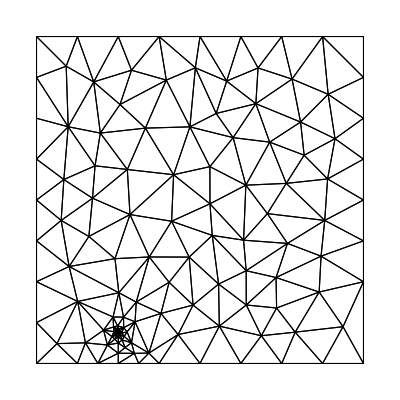
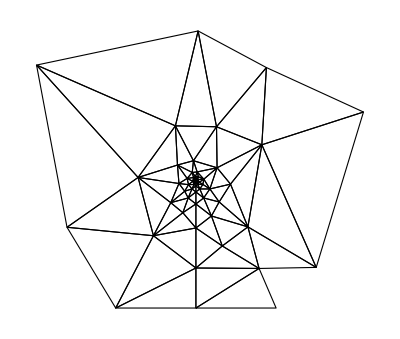

Integration time over disk

{3.04688,0.000460287}

Integration time over tip mesh

{0.046875,0.000659927}

```mathematica
msh=regionMesh[
rectangulraBoundary[{0.25,0.1}],
defaultMeshRefinmentFunc[{0.25,0.1},0.1]
]
tipMsh=GetTipMesh[msh,0.1]
sol=solution[msh]
Row[{msh["mesh"]["Wireframe"],tipMsh["Wireframe"]}]
Print["Integration time over disk"]
Timing@TipCircleIntegral[sol,{0.25,0.1}]//Quiet
Print["Integration time over tip mesh"]
Timing@NIntegrate[sol[x,y],{x,y}∈tipMsh,
AccuracyGoal->20,
PrecisionGoal->15, 
MaxRecursion->45
]
```

## What about AccuracyGoal, PrecisionGoal, MaxRecursion and WorkingPrecision?

<|tip→{0.25,0.1},mesh→ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<1944>]}]|>

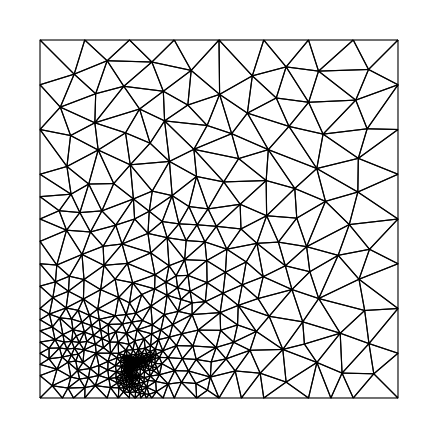

InterpolatingFunction[…]

```mathematica
msh=regionMesh[
rectangulraBoundary[{0.25,0.1}],
defaultMeshRefinmentFunc[{0.25,0.1},0.01]
]
msh["mesh"]["Wireframe"]
sol=solution[msh]
```

```mathematica
accuracyTable=Table[
Timing@NIntegrate[
sol[x,y],{x,0,1},{y,0,1},
AccuracyGoal->accuracyGoal,
PrecisionGoal->precisionGoal, 
MaxRecursion->40,
WorkingPrecision->16]//Quiet,
{precisionGoal,Range[1,15,1]},
{accuracyGoal,Range[1,15,1]}
];
```

NIntegrate::inumr: The integrand solution[{0.25,0.1},<|tip→{0.25,0.1},mesh→ElementMesh[{{0.,1.},{0.,1.}},{TriangleElement[<1944>]}]|>][x,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::accg: Value of option AccuracyGoal -> accuracyGoal is not Automatic, Infinity, or a machine-sized real or integer.

```mathematica
Row[{ListPlot3D[
accuracyTable[[All,All,2]],
PlotRange->All,
AxesLabel->{"Precision Goal","Accuracy Goal","Value"},
MeshFunctions->{#3&},
PlotTheme->"Scientific",
ImageSize->Medium
],ListPlot3D[accuracyTable[[All,All,1]],PlotRange->All,AxesLabel->{"Precision Goal","Accuracy Goal","Time"},ImageSize->Medium]}]
```

-Graphics3D--Graphics3D-

```mathematica
MatrixPlot
```

## Now lets consider series parameters

```mathematica
tipPoint={0.25,0.1};
seriesLimit=seriesParameters[
solution[tipPoint,
regionMesh[
rectangulraBoundary[tipPoint],
defaultMeshRefinmentFunc[tipPoint,#]
]
],
tipPoint]&/@Table[0.2^i,{i,1,7,0.5}]//Quiet
```

{{0.102095,0.0450131,0.123538},{0.101992,0.0454267,0.122371},{0.101856,0.0456871,0.125619},{0.101574,0.0460492,0.128888},{0.101742,0.0455131,0.129703},{0.101791,0.045499,0.131093},{0.101847,0.0454689,0.131065},{0.101865,0.0454652,0.131008},{0.101876,0.0454656,0.131003},{0.101881,0.0454659,0.131006},{0.101883,0.0454659,0.131005},{0.101882,0.0454658,0.131004},{0.101884,0.0454659,0.131004}}

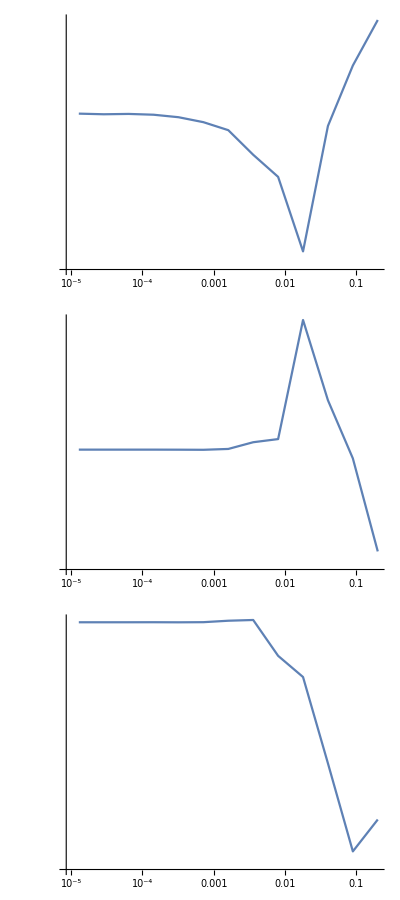

```mathematica
ListLogLogPlot[Transpose[{Table[0.2^i,{i,1,7,0.5}],#}],Joined->True,ImageSize->Medium]&/@Transpose@seriesLimit//Column
```

#### Lets change accuracy and will see if the value will be changed

```mathematica
seriesLimit2=seriesParameters[
solution[tipPoint,
regionMesh[
rectangulraBoundary[tipPoint],
defaultMeshRefinmentFunc[tipPoint,0.00001]
],
#
],
tipPoint,#]&/@Range[1,16]//Quiet
```

{{0.101965,0.0454797,0.42065},{0.101965,0.0454797,0.42065},{0.101965,0.0454797,0.42065},{0.101965,0.0454797,0.42065},{0.101965,0.0454797,0.42065},{0.331691,0.0454797,0.42065},{0.081789,0.0454797,0.42065},{0.0999347,0.106637,0.42065},{0.101834,0.0491125,0.42065},{0.101743,0.035761,0.163819},{0.101884,0.0454551,0.133035},{0.101884,0.0454591,0.130715},{0.101884,0.0454664,0.130974},{0.101884,0.0454659,0.131004},{0.101884,0.0454659,0.131004},{0.101884,0.0454659,0.131004}}

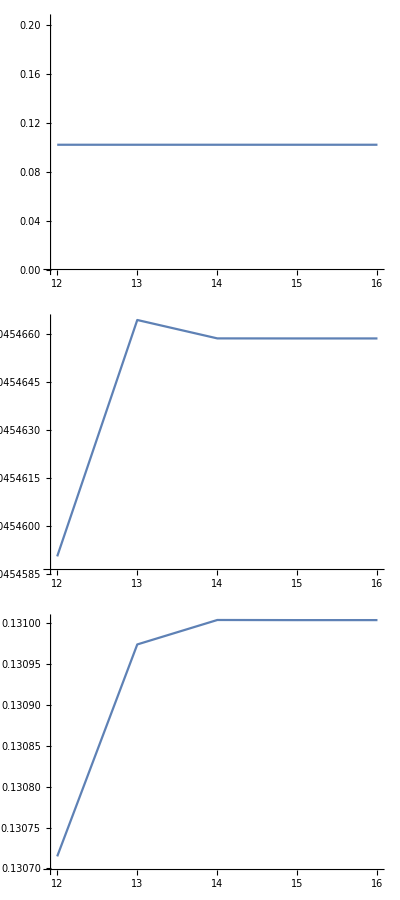

```mathematica
ListPlot[Transpose[{Range[12,16],#[[12;;-1]]}],Joined->True,ImageSize->Medium,PlotRange->All]&/@Transpose@seriesLimit2//Column
```